```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={Element[{mMu,hbarc2, GF, M, x,L, Ue42, deltam2},PositiveReals]};
```

```mathematica
$Assumptions={Element[{Gv, Ga},Reals]};
P[Enu_, Ue42_, deltam2_] := 1 - 4* (Ue42-Ue42^2)*Sin[1.267*deltam2*L/Enu]^2
```

```mathematica
EeFlux[Enu_]:=192/mMu*(Enu/mMu)^2(1/2 - Enu/mMu)*P[Enu,Ue42,deltam2](* E^-1 (1/MeV) *)
```

```mathematica
TtoQ[T_]:=Sqrt[2 M T + T^2] / hbarc (* E (1/fm after hbarc) *)
```

```mathematica
rnToR0[rn_]:=Sqrt[5/3 *(rn^2-3s^2)] (* 1/E same dimenstions as rn and s *)
Sqrt[6.12536^2*3/5+3s^2]
```

√(22.512+3 s^2)

```mathematica
rnToR0[4.77305]
```

√(5/3) √(22.782-3 s^2)

```mathematica
Series[SphericalBesselJ[1,x],{x,∞,3}]//Normal//Simplify
```

(-x Cos[x]+Sin[x])/x^2

```mathematica
J1[x_]:=(-x Cos[x]+Sin[x])/x^2
```

```mathematica
HelmFF[Q_]:=3*J1[Q*rnToR0[rn]]/(Q*rnToR0[rn])*Exp[-Q^2 * s^2/2] (* unitless *)
```

```mathematica
F[T_]:=HelmFF[TtoQ[T]] (* unitless *)
```

```mathematica
XSection[Enu_,Er_]:=hbarc2 GF^2*M/(2 Pi) F[Er]^2((Gv+Ga)^2+(Gv-Ga)^2(1-Er/Enu)^2-(Gv^2-Ga^2)M Er/Enu^2) (* E^-3 (cm^2 / MeV after hbarc2)*)
```

```mathematica
eRSpectrum[Er_]:=Integrate[EeFlux[ENu]*XSection[ENu,Er],{ENu, Sqrt[M*Er/2], mMu/2}] (* E^-3 (cm^2 / MeV after hbarc) *)
```

```mathematica
eRSpectrum[x]
```

$Aborted

```mathematica
smear[x_,e_]:=(a/e*(1+b*e))^(1+b*e)/Gamma[1+b*e]x^(b*e) Exp[-a/e(1+b*e) x]
```

```mathematica
Integrate[smear[x,e],{x,0,Infinity}]
```

ConditionalExpression[1., Re[1/e]>-9560.&&Re[e]>-0.000104603]

```mathematica
smear[10,0.002]
```

0.000136269

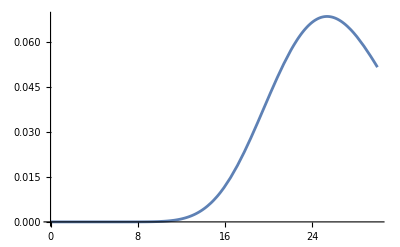

```mathematica
Plot[smear[x, 0.002],{x,0,30}]
```

```mathematica
eRSpectrum[0.002]
```

2.227×10^-36

```mathematica
Smeared[x_]:=NIntegrate[eRSpectrum[Er]smear[x,Er],{Er,0,Infinity}]
```

```mathematica
Smeared[10]
```

2.00035×10^-40

```mathematica
NIntegrate[eRSpectrum[Er] smear[10,Er],{Er,0,∞}]
```

2.00035×10^-40

1.67833×10^-40

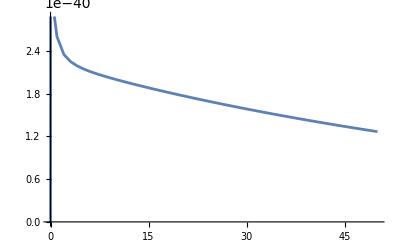

```mathematica
1.6783270373945175*^-40
Plot[Smeared[x],{x,0,50}]
```

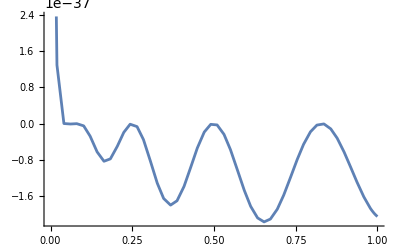

```mathematica
Plot[eRSpectrum[x],{x,0,1}]
```

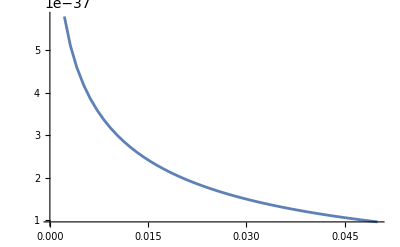

```mathematica
Plot[Smeared[x],{x,0.0001,0.05}]
```

```mathematica
Gv:=0.0298*55-0.5117*78
```

```mathematica
Ga:=0
```

```mathematica
M:=123800.645 (* MeV *)
```

```mathematica
GF :=1.16637*^-11 (* MeV^-2 *)
```

```mathematica
mMu := 105.6583755  (* MeV *)
```

```mathematica
s:= 0.3 (* fm *)
```

```mathematica
rn:=4.77305 (* fm *)
```

```mathematica
a:=0.0749/1000
```

```mathematica
b:=9.56*1000
```

```mathematica
hbarc2:=3.894×10^-22 (*cm^2 MeV^2*)
hbarc := 197.327 (* fm MeV *)
```

```mathematica
200/M
```

0.0016155

```mathematica
XSection[30, 0.00245]
```

```mathematica
eRSpectrum[x]
```

(6.80944×10^-34 ⅇ^((-0.572298-2.31137×10^-6 x) x) (41.9451-5583.43 x+35050.1 x^(3/2)-61794.6 x^2-332.155 x^(5/2)+1. x^3) SphericalBesselJ[1,0.0310417 √(x (247601.+x))]^2)/(x (247601.+x))

```mathematica
eRSpectrum[0.03]
```

6.56734×10^-38

```mathematica
XSection[16,0.00091]
```

2.28213×10^-36

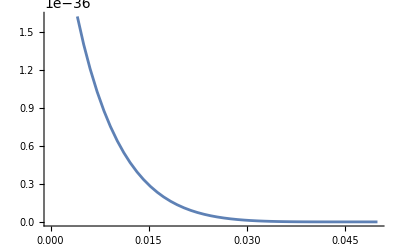

```mathematica
Plot[eRSpectrum[x],{x,0,0.05}]
```